# Visualization of WCG elongation link

## Program

```mathematica
withG[currentList_List,currentG_Integer]:=Module[{len,prevG},
prevG=currentG-5;
len=Length[currentList];
Table[Map[prevG[#]->currentG[n]&,currentList[[n]]],{n,len}]
]
```

```mathematica
WCGlinkwithG[currentList_List,currentG_Integer]:=Tally[Flatten[withG[currentList,currentG]]]
```

```mathematica
WCGlinkToGraph[link_]:=Graph[Map[DirectedEdge[#[[1,1]],#[[1,2]],#[[2]]]&,link]]
```

## Data

```mathematica
refdatadir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

```mathematica
datafile="elongationMat.save"
```

elongationMat.save

```mathematica
(*Get[datadir<>datafile];*)
```

```mathematica
wcgN={2353,3851,4624,5729,7020,8446,9401,10026,10687,11361,12147,13000,13398,13643,14933}
```

{2353,3851,4624,5729,7020,8446,9401,10026,10687,11361,12147,13000,13398,13643,14933}

```mathematica
genEnd=Table[n,{n,1950,2020,5}]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
Do[WCGcount[genEnd[[n]]]=wcgN[[n]],{n,1,15}]
```

```mathematica
WCGcount[1950]
```

2353

## Data reform

```mathematica
(*WCGElink["All"]=Flatten[Table[WCGlinkwithG[elMat[n],n],{n,1955,2020,5}],1];*)
```

```mathematica
wcgsavefile="WCGELinkAll.save"
```

WCGELinkAll.save

```mathematica
(*Save[datadir<>wcgsavefile,WCGElink]*)
```

以下はメモリー消費大

```mathematica
(*Do[elMatwithG[n]=withG[elMat[n],n];,{n,1955,2020,5}]*)
```

```mathematica
Get[refdatadir<>wcgsavefile];
```

## Visualization type:1

### >= 10

```mathematica
WCGElink[10]=Cases[WCGElink["All"],x_/;x[[2]]>=10];
```

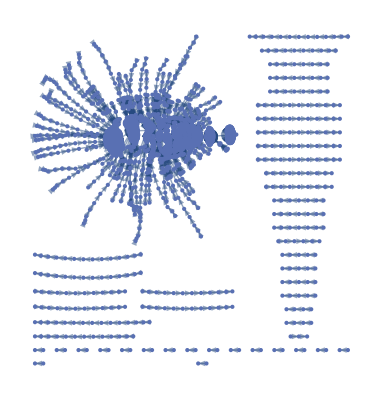

```mathematica
WCGelgraph[10]=WCGlinkToGraph[WCGElink[10]]
```

```mathematica
vc10=Map[#->{#[[0]],#[[1]]/WCGcount[#[[0]]]*100}&,WCGelgraph[10]//VertexList];
```

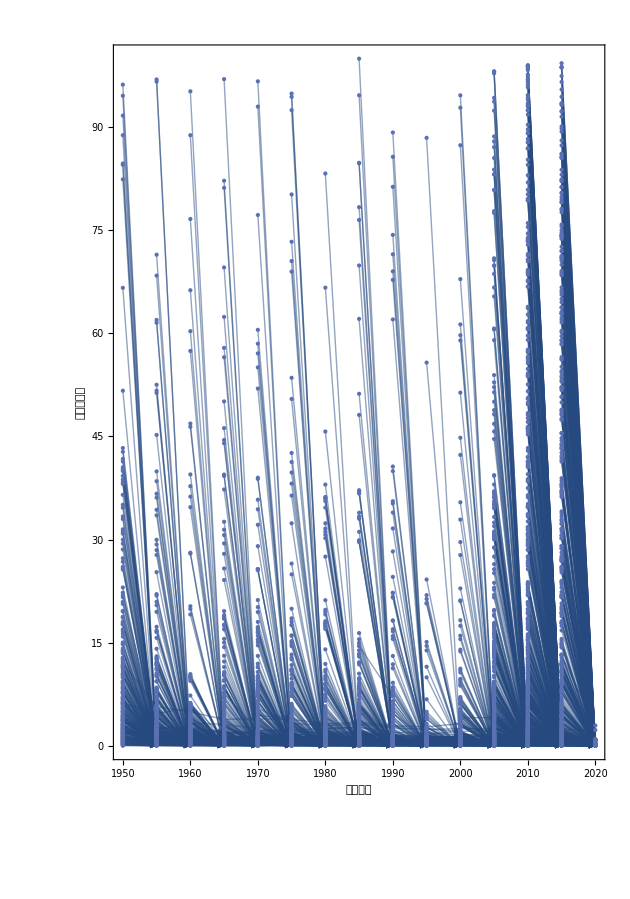

```mathematica
gp10=GraphPlot[Graph[WCGelgraph[10],VertexCoordinates->vc10,Frame->True,FrameTicks->{Automatic,Automatic}],FrameLabel->{"累積世代","順位百分率"}]
```

## Visualization type:HeatMap

### >= 10

エッジに色をつける

```mathematica
WCGElink[10]=Cases[WCGElink["All"],x_/;x[[2]]>=10];
```

```mathematica
vc10=Map[#->{#[[0]],#[[1]]/WCGcount[#[[0]]]*100}&,WCGelgraph[10]//VertexList];
```

```mathematica
max=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Max
```

1.99873×10^8

```mathematica
maxl=Map[N[Log[#[[3]]]]&,EdgeList[WCGelgraph[10]]]//Max
```

19.1132

```mathematica
myColorData[v_]:=Which[10<=v&&v<20,Red,20<=v,Blue]
```

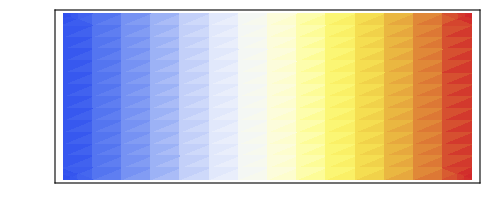
-Graphics-
弱    <-結合->    強

```mathematica
colorscale=Grid[{{DensityPlot[x,{x,0,1},{y,0,0.1},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->False,AspectRatio->Automatic,FrameTicks->{{None,None},{None,None}}]},{"弱    <-結合->    強"}}]
```

```mathematica
es=Table[EdgeList[WCGelgraph[10]][[n]]->ColorData["TemperatureMap"][(EdgeList[WCGelgraph[10]][[n]][[3]]-10)/(maxl-10)],{n,Length[EdgeList[WCGelgraph[10]]]}]
```

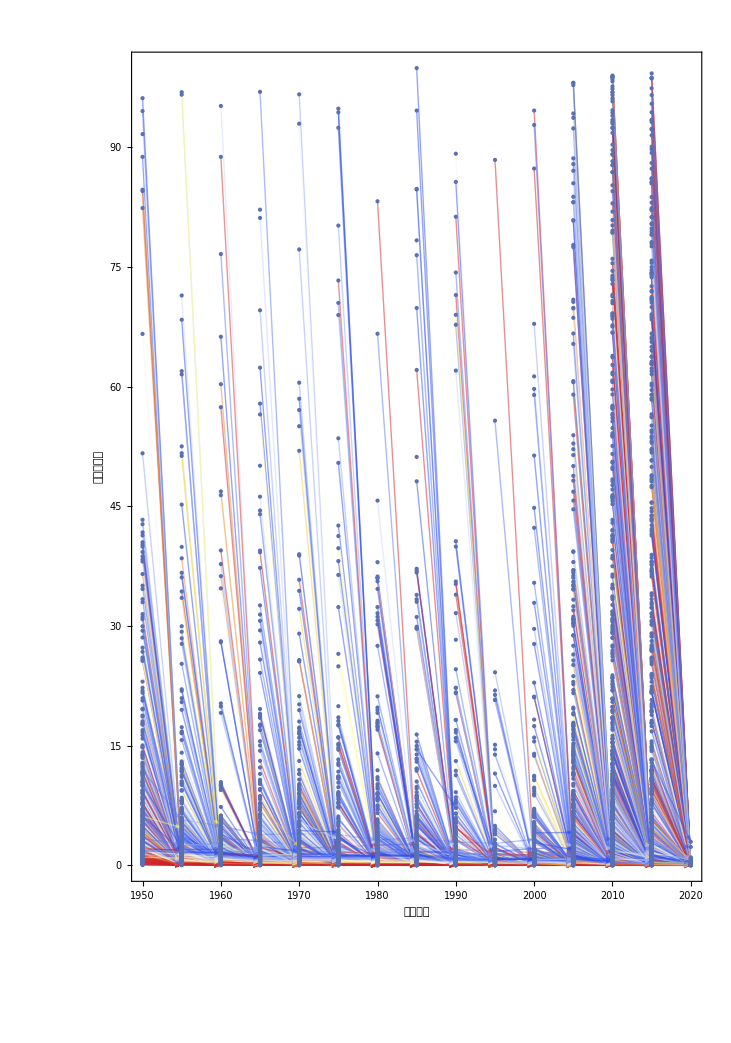

```mathematica
gp10=GraphPlot[Graph[WCGelgraph[10],VertexCoordinates->vc10,EdgeStyle->es,Frame->True,FrameTicks->{Automatic,Automatic}],FrameLabel->{"累積世代","順位百分率"}]
```

## Visualization type:5 colors

### >= 10

```mathematica
WCGElink[10]=Cases[WCGElink["All"],x_/;x[[2]]>=10];
```

```mathematica
vc10=Map[#->{#[[0]],#[[1]]/WCGcount[#[[0]]]*100}&,WCGelgraph[10]//VertexList];
```

```mathematica
max=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Max
min=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Min
```

1.99873×10^8

10.

```mathematica
myColorData[v_]:=Which[v>=40,Red,40>v&&v>=24,RGBColor[1,0.4,0],24>v&&v>=16,RGBColor[0.8,0.6,0.3],16>v&&v>= 12,RGBColor[0.2,0.6,0.6], 12>v&&v>=10,RGBColor[0.2,0.3,1]]
```

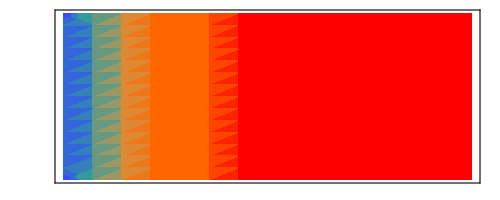
-Graphics-
弱    <-結合->    強

```mathematica
colorscale=Grid[{{DensityPlot[x,{x,min,80},{y,0,10},ColorFunction->myColorData,ColorFunctionScaling->False,AspectRatio->Automatic,FrameTicks->{{None,None},{None,None}}]},{"弱    <-結合->    強"}}]
```

```mathematica
es=Table[EdgeList[WCGelgraph[10]][[n]]->myColorData[(EdgeList[WCGelgraph[10]][[n]][[3]])],{n,Length[EdgeList[WCGelgraph[10]]]}]
```

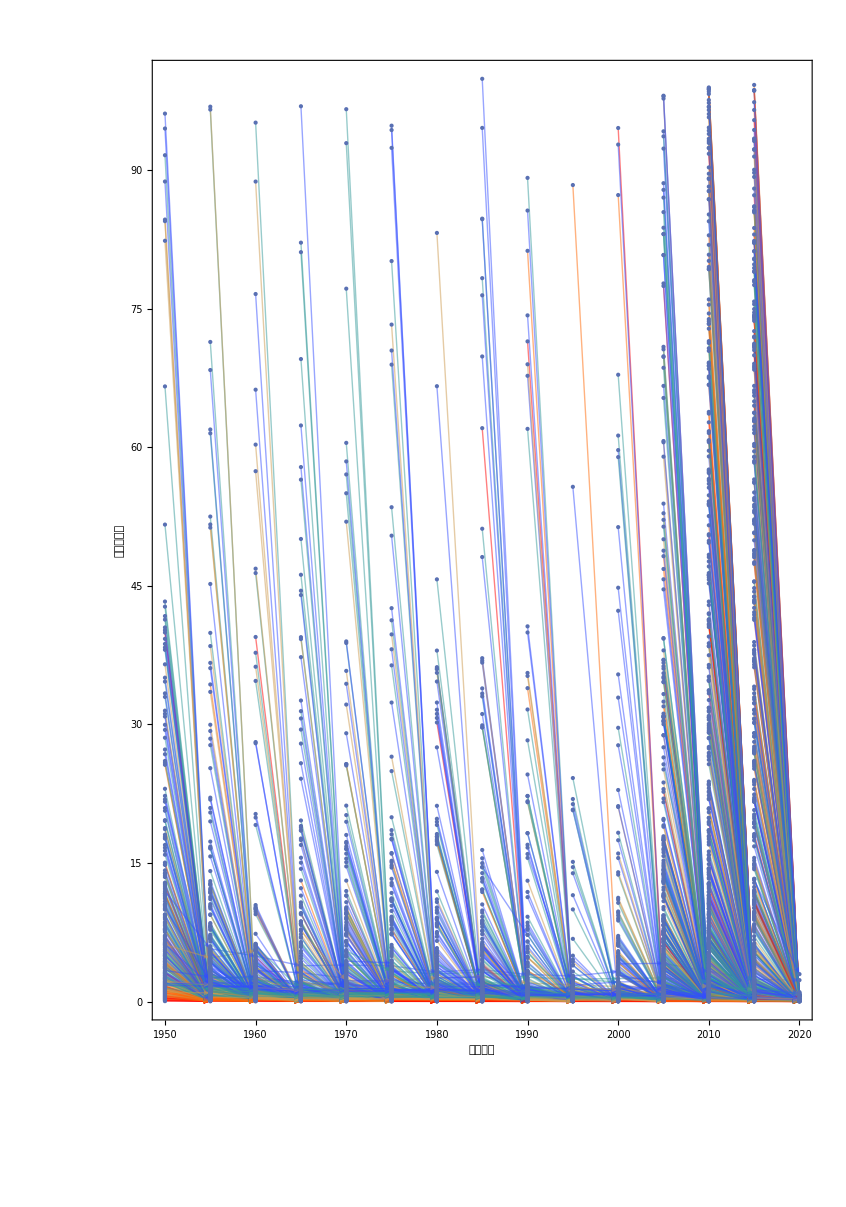

```mathematica
gp10=GraphPlot[Graph[WCGelgraph[10],VertexCoordinates->vc10,EdgeStyle->es,Frame->True,FrameTicks->{Automatic,Automatic}],FrameLabel->{"累積世代","順位百分率"}]
```

## Visualization type:4 colors

### >= 10

```mathematica
WCGElink[10]=Cases[WCGElink["All"],x_/;x[[2]]>=10];
```

```mathematica
vc10=Map[#->{#[[0]],#[[1]]/WCGcount[#[[0]]]*100}&,WCGelgraph[10]//VertexList];
```

```mathematica
max=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Max
min=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Min
```

1.99873×10^8

10.

```mathematica
myColorData[v_]:=Which[v>=45,Red,45>v&&v>=25,RGBColor[1,0.5,0],25>v&&v>=15,RGBColor[0.9,0.8,0], 15>v&&v>=10,RGBColor[0.3,0.6,1]]
```

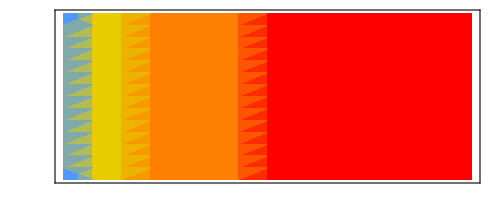
-Graphics-
弱    <-結合->    強

```mathematica
colorscale=Grid[{{DensityPlot[x,{x,min,80},{y,0,10},ColorFunction->myColorData,ColorFunctionScaling->False,AspectRatio->Automatic,FrameTicks->{{None,None},{None,None}}]},{"弱    <-結合->    強"}}]
```

```mathematica
es=Table[EdgeList[WCGelgraph[10]][[n]]->myColorData[(EdgeList[WCGelgraph[10]][[n]][[3]])],{n,Length[EdgeList[WCGelgraph[10]]]}]
```

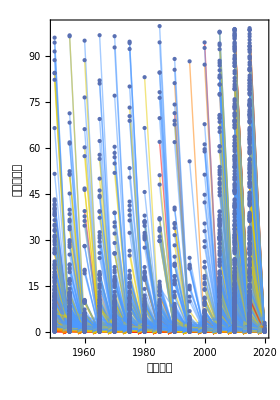

```mathematica
gp10=GraphPlot[Graph[WCGelgraph[10],VertexCoordinates->vc10,EdgeStyle->es,Frame->True,FrameTicks->{Automatic,Automatic}],FrameLabel->{"累積世代","順位百分率"}]
```